```mathematica
(*求圆的一对对称点坐标*)
```

```mathematica
a=(r2-r1)/d;b=√(1-a^2);
r3=(√(d^2-(r2-r1)^2))/2;
Solve[(b*(r2+r1)/2)^2+(y+a*(r2+r1)/2)^2==r3^2,y]
```

{{y→(r1^2-r2^2-√(d^4-2 d^2 r1^2+r1^4-2 d^2 r2^2-2 r1^2 r2^2+r2^4))/(2 d)},{y→(r1^2-r2^2+√(d^4-2 d^2 r1^2+r1^4-2 d^2 r2^2-2 r1^2 r2^2+r2^4))/(2 d)}}

```mathematica
(*求分式变换式的系数*)
```

```mathematica
r1=2;r2=2;d=20;
z1=(r1^2-r2^2-√(d^4-2 d^2 r1^2+r1^4-2 d^2 r2^2-2 r1^2 r2^2+r2^4))/(2 d)ⅈ;
z2=(r1^2-r2^2+√(d^4-2 d^2 r1^2+r1^4-2 d^2 r2^2-2 r1^2 r2^2+r2^4))/(2 d)ⅈ;
z=-ⅈ*(d/2-r1);
Solve[k*(z-z1)/(z-z2)==1,k]
```

{{k→(-2-√6)/(-2+√6)}}

```mathematica
Clear[z]
```

```mathematica
(*Subscript[求O, 2] 的半径*)
```

```mathematica
k=(-2-√6)/(-2+√6);
w=k*(z-z1)/(z-z2);
R2=Norm[w/.z->ⅈ(d/2-r2)]
```

((2+√6) (8+4 √6))/((-2+√6) (-8+4 √6))

```mathematica
Clear[w,R2]
```

```mathematica
(*用分式线性变换求电势*)
```

192/((-2+√6) (x^2+(-4 √6+y)^2))+(96 √6)/((-2+√6) (x^2+(-4 √6+y)^2))-(2 x^2)/((-2+√6) (x^2+(-4 √6+y)^2))-(√6 x^2)/((-2+√6) (x^2+(-4 √6+y)^2))-(2 y^2)/((-2+√6) (x^2+(-4 √6+y)^2))-(√6 y^2)/((-2+√6) (x^2+(-4 √6+y)^2))

-(48 x)/((-2+√6) (x^2+(-4 √6+y)^2))-(16 √6 x)/((-2+√6) (x^2+(-4 √6+y)^2))

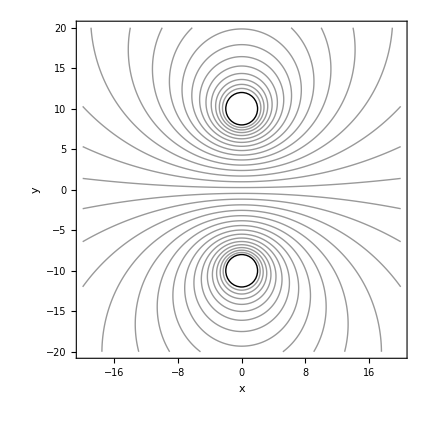

```mathematica
z=x+ⅈ*y;w=k*(z-z1)/(z-z2);V=10;
ξ=ComplexExpand[Re[w]]
η=ComplexExpand[Im[w]]
r=√(ξ^2+η^2);R2=((2+√6) (8+4 √6))/((-2+√6) (-8+4 √6));
φ[x_,y_]:=V*Log[r]/Log[R2]
ContourPlot[φ[x,y],{x,-d,d},{y,-d,d},PlotPoints->100,ContourShading->False,Contours->30,Axes->True,AxesLabel->{"x","y"},Epilog->{Circle[{0,-d/2},r1],Circle[{0,d/2},r2]},PlotRange->{0,V}]
```

```mathematica
Clear[φ]
```

```mathematica
(*求导体表面的电荷面密度分布*)
```

(10 √6)/(ArcCosh[49] (5+Sin[θ]))

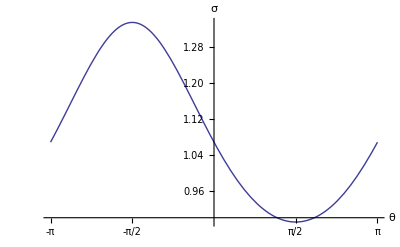

```mathematica
n={Cos[θ],Sin[θ]};p={0,d/2}+r2*n;
field={-D[φ[x,y],x],-D[φ[x,y],y]};
density=((field/.{x->p[[1]],y->p[[2]]}).n)//FullSimplify
Plot[density,{θ,-π,π},PlotRange->All,Ticks->{{-π,-π/2,π/2,π},Automatic},AxesLabel->{"θ","σ"}]
```